```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap3D[];
sizes={32,32,32};
max=4ho;
min=-max;
timeStep=0.0001;
k=-0.57;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{32,32,32} | 3 | 32768 | {4,4,4} | {-4,-4,-4} | {8/31,8/31,8/31} | {(31 π)/128,(31 π)/128,(31 π)/128} | {(31 π)/8,(31 π)/8,(31 π)/8}

time | energies | moments | misc
(0) | (total | 1.2726
kinetic | 0.75
potential | 0.75
contact | -0.227397
virial | -0.682192) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 0.707107
sigmaY | 0.707107
sigmaZ | 0.707107
norm | 1.) | (steps | 0
A0 | 0.423392)

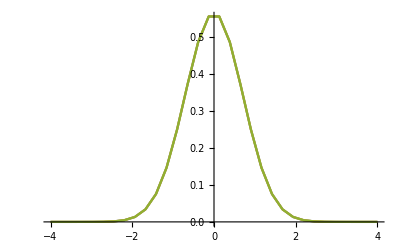

```mathematica
calcAllTable
plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{572.743,Null}

time | energies | moments | misc
(10.) | (total | 1.17434
kinetic | 1.41533
potential | 0.421988
contact | -0.662972
virial | -0.00224179) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 0.530401
sigmaY | 0.530401
sigmaZ | 0.530401
norm | 1.) | (steps | 100000
A0 | 0.810524)

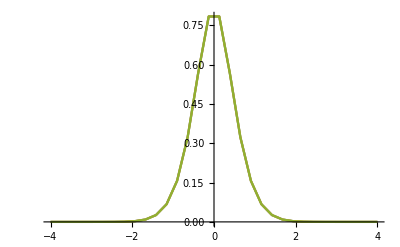

```mathematica
calcAllTable
plotProjections
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 1.2726 | 0.75 | 0.75 | -0.227397 | -0.682192
1. | 1.18878 | 1.05175 | 0.549489 | -0.41246 | -0.232857
2. | 1.17769 | 1.2109 | 0.483851 | -0.517065 | -0.0971004
3. | 1.17535 | 1.29487 | 0.455933 | -0.575451 | -0.0484761
4. | 1.1747 | 1.3425 | 0.441738 | -0.609536 | -0.0270899
5. | 1.17448 | 1.37102 | 0.433737 | -0.630279 | -0.0162664
6. | 1.1744 | 1.38875 | 0.428939 | -0.643295 | -0.0102552
7. | 1.17436 | 1.40005 | 0.425949 | -0.651636 | -0.00670399
8. | 1.17435 | 1.40737 | 0.424039 | -0.65706 | -0.00451765
9. | 1.17434 | 1.41216 | 0.4228 | -0.66062 | -0.00313391
10. | 1.17434 | 1.41533 | 0.421988 | -0.662972 | -0.00224179

```mathematica
reportMoments
```

time | meanX | meanY | meanZ | sigmaX | sigmaY | sigmaZ | norm
0 | 0 | 0 | 0 | 0.707107 | 0.707107 | 0.707107 | 1.
1. | 0 | 0 | 0 | 0.605249 | 0.605249 | 0.605249 | 1.
2. | 0 | 0 | 0 | 0.56795 | 0.56795 | 0.56795 | 1.
3. | 0 | 0 | 0 | 0.551321 | 0.551321 | 0.551321 | 1.
4. | 0 | 0 | 0 | 0.542671 | 0.542671 | 0.542671 | 1.
5. | 0 | 0 | 0 | 0.537734 | 0.537734 | 0.537734 | 1.
6. | 0 | 0 | 0 | 0.534752 | 0.534752 | 0.534752 | 1.
7. | 0 | 0 | 0 | 0.532885 | 0.532885 | 0.532885 | 1.
8. | 0 | 0 | 0 | 0.531689 | 0.531689 | 0.531689 | 1.
9. | 0 | 0 | 0 | 0.530911 | 0.530911 | 0.530911 | 1.
10. | 0 | 0 | 0 | 0.530401 | 0.530401 | 0.530401 | 1.